```mathematica
voltageData={{0.,0.},{0.05,0.62},{0.19,1.97},{0.25,2.65},{0.33,3.34},{0.66,6.72},{1.29,12.92},{1.93,19.33}}
```

{{0.,0.},{0.05,0.62},{0.19,1.97},{0.25,2.65},{0.33,3.34},{0.66,6.72},{1.29,12.92},{1.93,19.33}}

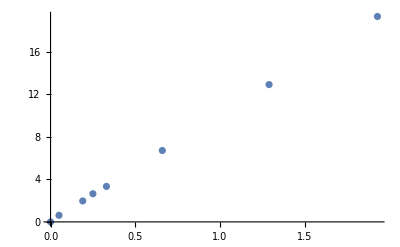

```mathematica
ListPlot[voltageData]
```

```mathematica
voltageFit=LinearModelFit[voltageData,x,x]
```

FittedModel[0.0849436+9.97244 x]

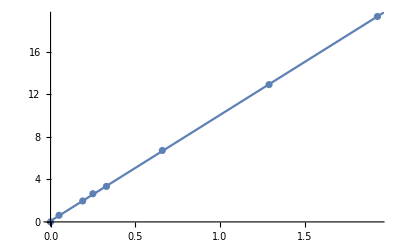

```mathematica
Show[ListPlot[voltageData],Plot[voltageFit[x],{x,0,2}]]
```

```mathematica
slope=9.97244;
```